# Project Euler Problem 15

For an n×n grid, travelling from top left to bottom right corner requires n right steps and n down steps. So the number of paths just the number of permutations: (2n)!/(n!)^2.

```mathematica
pathCount[n_]:=(2n)!/(n!)^2
```

```mathematica
pathCount[2]
```

6

```mathematica
pathCount[20]
```

137846528820

A more Mathematica-oriented challenge is to generate some sample paths:

```mathematica
randomPath[n_]:=Graphics[{Thick,Line[Accumulate[Prepend[RandomSample[Join[ConstantArray[{1,0},n],ConstantArray[{0,-1},n]]],{0,0}]]]},Frame->True,Axes->False,GridLines->{Range[0,n],-Range[0,n]},GridLinesStyle->Directive[Gray,Dotted],FrameTicks->False,FrameStyle->Directive[Gray,Thick],Background->LightGray]
```

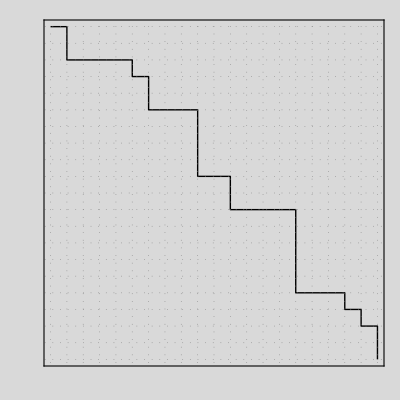

```mathematica
randomPath[20]
```